# Ph3 Set 8

## Jacob Snyder

## 5/22/19

```mathematica
randnums=Table[Round@Mod[MantissaExponent[N@1/7^(i)][[1]]*10^(6),10],{i,20}]
```

{7,2,5,3,0,6,7,7,9,3,3,6,1,4,4,6,6,5,8,5}

They look reasonably random.

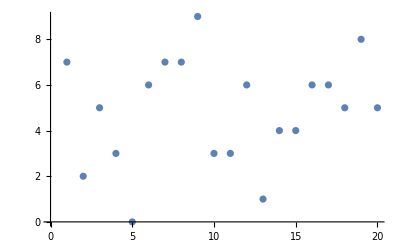

```mathematica
ListPlot@randnums
```

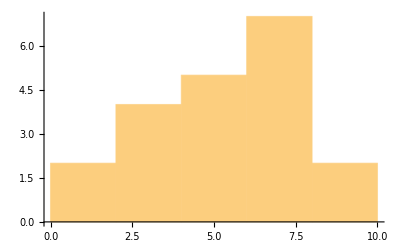

```mathematica
Histogram@randnums
```

It looks much less random when plotted as a histogram; we can see that the numbers between 0 and 2 and between 8 and 10 are much less frequently chosen.

```mathematica
RandomReal[{0,1}]
```

0.145634

```mathematica
RandomReal[{0,1}]
```

0.472807

```mathematica
RandomReal[{0,1}]
```

0.360859

```mathematica
SeedRandom[1]
RandomReal[{0,1}]
```

0.817389

```mathematica
SeedRandom[1]
RandomReal[{0,1}]
```

0.817389

```mathematica
SeedRandom[1]
RandomReal[{0,1}]
```

0.817389

```mathematica
N@Sqrt[22]/25
```

0.187617

Uncertainty is 0.187617, which is about 5% of Pi. Therefore we got lucky with the 1% error.
In order to get 1% accuracy, if we sample x points, then the number counted will be on average x(1-Pi/4) so the uncertainty in Pi will be 4*[x(1-Pi/4)]^(1/2)/x. If we set this equal to Pi/100, we get:

```mathematica
x=N@(((Pi/400)^2)/(1-Pi/4))^(-1)
```

3478.99

So we’d need 3479 points to consistently get 1% accuracy.

```mathematica
numpts=3479;
randomdata=RandomReal[{0,1},{numpts,2}];
N@4*Total@Map[If[#[[2]]^2>1-#[[1]]^2,0,1/numpts]&,randomdata]
```

3.12389